## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="FBA1";
fitLabel="p2_keq_1";
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;

(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Desktop/MASSef/";
kineticDataFileName =  "kinetic_data_MASSef.csv";

mainFolder = "fit_FBA1";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/MASSef/examples/FBA1/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{fdp,Null,Keq substrate}

{0.00016,Keq value}

{fdp,Km or S05 substrate}

{0.00002,Km or S05 value}

{{{fdp,Null}},kcat substrates}

{0.217,kcat value}

{fdp,Km or S05 substrate}

{0.00002,Km or S05 value}

{{{fdp,Null},{cit,0.011}},kcat substrates}

{3.17,kcat value}

{fdp,Km or S05 substrate}

{0.00007,Km or S05 value}

(fdp^c⇌dhap^c+g3p^c)^FBA1

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

Structure: 8-10

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp,Null | 0.00016 | 0.000152
0.000168 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00002 | 0.000019
0.000021 |  | M | 7.5 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00002 | 0.000018
0.000022 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00007 | 0.000058
0.000082 | cit | 0.011 | M | 8 | 30 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 0.412114 | 0.39882
0.423509 | 1/s | 8 | 37 | trishcl | 0.05 | 
1 | fdp | Null
cit | 0.011 | 6.02029 | 5.71642
6.32415 | 1/s | 8 | 37 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

(*KeqPriorities = {2};
kmPriorities = {0,10,10};
s05Priorities = Null;
kcatPriorities = {2,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;*)

KeqPriorities = {1};
kmPriorities = {0,1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(fdp^c⇌dhap^c+g3p^c)^FBA1

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

Structure: 8-10

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp,Null | 0.00016 | 0.000152
0.000168 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00002 | 0.000018
0.000022 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00007 | 0.000058
0.000082 | cit | 0.011 | M | 8 | 30 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 0.412114 | 0.39882
0.423509 | 1/s | 8 | 37 | trishcl | 0.05 | 
1 | fdp | Null
cit | 0.011 | 6.02029 | 5.71642
6.32415 | 1/s | 8 | 37 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Construct Module and Set Up Comparison Equations

```mathematica
haldaneRatiosList
```

{(k_FBA12^⟶ k_FBA14^⟶ k_FBA15^⟶ k_FBA18^⟶)/(k_FBA12^⟵ k_FBA14^⟵ k_FBA15^⟵ k_FBA18^⟵),(k_FBA13^⟶ k_FBA16^⟶ k_FBA17^⟶ k_FBA19^⟶)/(k_FBA13^⟵ k_FBA16^⟵ k_FBA17^⟵ k_FBA19^⟵)}

### Construct enzyme module

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

```mathematica
catalyticBranch={"E_FBA1[c] + fdp[c] <=> E_FBA1[c]&fdp",
				"E_FBA1[c]&fdp <=> E_FBA1[c]&dhap&g3p",
				"E_FBA1[c]&dhap&g3p <=> E_FBA1[c]&dhap + g3p[c]",
				"E_FBA1[c]&dhap <=> E_FBA1[c] + dhap[c]",
				
				"E_FBA1[c] + cit[c] <=> E_FBA1[c]&cit",
				"E_FBA1[c]&cit + fdp[c] <=> E_FBA1[c]&cit&fdp",
				"E_FBA1[c]&cit&fdp <=> E_FBA1[c]&cit&dhap&g3p",
				"E_FBA1[c]&cit&dhap&g3p <=> E_FBA1[c]&cit&dhap + g3p[c]",
				"E_FBA1[c]&cit&dhap <=> E_FBA1[c]&cit + dhap[c]"};


enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((FBA1^c)_^+cit^c⇌(FBA1^c&cit^c)_^)^FBA11,((FBA1^c)_^+fdp^c⇌(FBA1^c&fdp^c)_^)^FBA12,((FBA1^c&cit^c)_^+fdp^c⇌(FBA1^c&cit^c&fdp^c)_^)^FBA13,((FBA1^c&dhap^c)_^⇌(FBA1^c)_^+dhap^c)^FBA14,((FBA1^c&fdp^c)_^⇌(FBA1^c&dhap^c&g3p^c)_^)^FBA15,((FBA1^c&cit^c&dhap^c)_^⇌(FBA1^c&cit^c)_^+dhap^c)^FBA16,((FBA1^c&cit^c&fdp^c)_^⇌(FBA1^c&cit^c&dhap^c&g3p^c)_^)^FBA17,((FBA1^c&dhap^c&g3p^c)_^⇌(FBA1^c&dhap^c)_^+g3p^c)^FBA18,((FBA1^c&cit^c&dhap^c&g3p^c)_^⇌(FBA1^c&cit^c&dhap^c)_^+g3p^c)^FBA19}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((FBA1^c)_^+fdp^c⇌(FBA1^c&fdp^c)_^)^FBA12,Overscript[(FBA1^c&dhap^c)_^⇌(FBA1^c)_^+dhap^c, FBA14],((FBA1^c&fdp^c)_^⇌(FBA1^c&dhap^c&g3p^c)_^)^FBA15,Overscript[(FBA1^c&dhap^c&g3p^c)_^⇌(FBA1^c&dhap^c)_^+g3p^c, FBA18]};
catalyticReactionsSet2={((FBA1^c&cit^c)_^+fdp^c⇌(FBA1^c&cit^c&fdp^c)_^)^FBA13,Overscript[(FBA1^c&cit^c&dhap^c)_^⇌(FBA1^c&cit^c)_^+dhap^c, FBA16],((FBA1^c&cit^c&fdp^c)_^⇌(FBA1^c&cit^c&dhap^c&g3p^c)_^)^FBA17,Overscript[(FBA1^c&cit^c&dhap^c&g3p^c)_^⇌(FBA1^c&cit^c&dhap^c)_^+g3p^c, FBA19]};
catalyticReactionsSetsList = {catalyticReactionsSet1, catalyticReactionsSet2};
```

```mathematica
catalyticReactionsSet1={((FBA1^c)_^+fdp^c⇌(FBA1^c&fdp^c)_^)^FBA11,Overscript[(FBA1^c&dhap^c)_^⇌(FBA1^c)_^+dhap^c, FBA12],((FBA1^c&fdp^c)_^⇌(FBA1^c&dhap^c&g3p^c)_^)^FBA13,Overscript[(FBA1^c&dhap^c&g3p^c)_^⇌(FBA1^c&dhap^c)_^+g3p^c, FBA14]};
catalyticReactionsSet2={Overscript[(FBA1^c)_^(cit^c)+fdp^c⇌(FBA1^c&fdp^c)_^(cit^c), FBA11$3],Overscript[(FBA1^c&dhap^c)_^(cit^c)⇌(FBA1^c)_^(cit^c)+dhap^c, FBA12$3],Overscript[(FBA1^c&fdp^c)_^(cit^c)⇌(FBA1^c&dhap^c&g3p^c)_^(cit^c), FBA13$3],Overscript[(FBA1^c&dhap^c&g3p^c)_^(cit^c)⇌(FBA1^c&dhap^c)_^(cit^c)+g3p^c, FBA14$3]};
catalyticReactionsSetsList = {enzymeModelOrig["Reactions"]};
```

## Set up rate equations

```mathematica
deleteDirectoryContents[inputPath];
```

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=30;
assumedSaturatingConc = 1;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites,assumedSaturatingConc];
```

{fdp^c→0}

{dhap^c→0,g3p^c→0}

{fdp^c→1}

{dhap^c→1,g3p^c→1}

Added inhibition reactions:

{}

Loading flux equation...

Loading absolute rate forward equation...

Loading absolute rate reverse equation...

Loading relative rate forward equation...

Loading relative rate reverse equation...

Loading relative rate reverse equation...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

Elementary reactions

```mathematica
enzymeModel["Reactions"]
```

{((FBA1^c)_^+cit^c⇌(FBA1^c&cit^c)_^)^FBA11,((FBA1^c)_^+fdp^c⇌(FBA1^c&fdp^c)_^)^FBA12,((FBA1^c&cit^c)_^+fdp^c⇌(FBA1^c&cit^c&fdp^c)_^)^FBA13,((FBA1^c&dhap^c)_^⇌(FBA1^c)_^+dhap^c)^FBA14,((FBA1^c&fdp^c)_^⇌(FBA1^c&dhap^c&g3p^c)_^)^FBA15,((FBA1^c&cit^c&dhap^c)_^⇌(FBA1^c&cit^c)_^+dhap^c)^FBA16,((FBA1^c&cit^c&fdp^c)_^⇌(FBA1^c&cit^c&dhap^c&g3p^c)_^)^FBA17,((FBA1^c&dhap^c&g3p^c)_^⇌(FBA1^c&dhap^c)_^+g3p^c)^FBA18,((FBA1^c&cit^c&dhap^c&g3p^c)_^⇌(FBA1^c&cit^c&dhap^c)_^+g3p^c)^FBA19}

Equation used to fit the forward kcat

```mathematica
absoluteRateForward
```

(fdp^c FBA1_total_Global k_FBA14^⟶ k_FBA16^⟶ (cit^c k_FBA11^⟶ k_FBA13^⟶ k_FBA17^⟶ (k_FBA15^⟶ k_FBA18^⟶+k_FBA12^⟵ (k_FBA15^⟵+k_FBA18^⟶)) k_FBA19^⟶+k_FBA11^⟵ k_FBA12^⟶ k_FBA15^⟶ k_FBA18^⟶ (k_FBA17^⟶ k_FBA19^⟶+k_FBA13^⟵ (k_FBA17^⟵+k_FBA19^⟶))))/(k_FBA11^⟵ (k_FBA14^⟶ k_FBA15^⟶ k_FBA18^⟶+k_FBA12^⟵ k_FBA14^⟶ (k_FBA15^⟵+k_FBA18^⟶)+fdp^c k_FBA12^⟶ (k_FBA15^⟶ k_FBA18^⟶+k_FBA14^⟶ (k_FBA15^⟵+k_FBA15^⟶+k_FBA18^⟶))) (k_FBA16^⟶ k_FBA17^⟶ k_FBA19^⟶+k_FBA13^⟵ k_FBA16^⟶ (k_FBA17^⟵+k_FBA19^⟶))+cit^c k_FBA11^⟶ (k_FBA14^⟶ k_FBA15^⟶ k_FBA18^⟶+k_FBA12^⟵ k_FBA14^⟶ (k_FBA15^⟵+k_FBA18^⟶)) (k_FBA16^⟶ k_FBA17^⟶ k_FBA19^⟶+k_FBA13^⟵ k_FBA16^⟶ (k_FBA17^⟵+k_FBA19^⟶)+fdp^c k_FBA13^⟶ (k_FBA17^⟶ k_FBA19^⟶+k_FBA16^⟶ (k_FBA17^⟵+k_FBA17^⟶+k_FBA19^⟶))))

r

```mathematica
relativeRateForward[[1]]//Simplify
```

(fdp^c (k_FBA11^⟵ k_FBA16^⟶ (k_FBA14^⟶ k_FBA15^⟶ k_FBA18^⟶+k_FBA12^⟵ k_FBA14^⟶ (k_FBA15^⟵+k_FBA18^⟶)+k_FBA12^⟶ (k_FBA15^⟶ k_FBA18^⟶+k_FBA14^⟶ (k_FBA15^⟵+k_FBA15^⟶+k_FBA18^⟶))) (k_FBA17^⟶ k_FBA19^⟶+k_FBA13^⟵ (k_FBA17^⟵+k_FBA19^⟶))+cit^c k_FBA11^⟶ k_FBA14^⟶ (k_FBA15^⟶ k_FBA18^⟶+k_FBA12^⟵ (k_FBA15^⟵+k_FBA18^⟶)) (k_FBA16^⟶ k_FBA17^⟶ k_FBA19^⟶+k_FBA13^⟵ k_FBA16^⟶ (k_FBA17^⟵+k_FBA19^⟶)+k_FBA13^⟶ (k_FBA17^⟶ k_FBA19^⟶+k_FBA16^⟶ (k_FBA17^⟵+k_FBA17^⟶+k_FBA19^⟶)))))/(k_FBA11^⟵ k_FBA16^⟶ (k_FBA14^⟶ k_FBA15^⟶ k_FBA18^⟶+k_FBA12^⟵ k_FBA14^⟶ (k_FBA15^⟵+k_FBA18^⟶)+fdp^c k_FBA12^⟶ (k_FBA15^⟶ k_FBA18^⟶+k_FBA14^⟶ (k_FBA15^⟵+k_FBA15^⟶+k_FBA18^⟶))) (k_FBA17^⟶ k_FBA19^⟶+k_FBA13^⟵ (k_FBA17^⟵+k_FBA19^⟶))+cit^c k_FBA11^⟶ k_FBA14^⟶ (k_FBA15^⟶ k_FBA18^⟶+k_FBA12^⟵ (k_FBA15^⟵+k_FBA18^⟶)) (k_FBA16^⟶ k_FBA17^⟶ k_FBA19^⟶+k_FBA13^⟵ k_FBA16^⟶ (k_FBA17^⟵+k_FBA19^⟶)+fdp^c k_FBA13^⟶ (k_FBA17^⟶ k_FBA19^⟶+k_FBA16^⟶ (k_FBA17^⟵+k_FBA17^⟶+k_FBA19^⟶))))

```mathematica
FBA1RateConsts=finalRateConsts
Export[inputPath<>"/"<>rxnName<>"_rateConsts.m",FBA1RateConsts, "MX"]
```

{k_FBA11^⟵,k_FBA11^⟶,k_FBA12^⟵,k_FBA12^⟶,k_FBA13^⟵,k_FBA13^⟶,k_FBA14^⟵,k_FBA14^⟶}

/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBA1/fit_FBA1/input/FBA1_rateConsts.m

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
fitLabel="new_lma_p2_keq_1";
```

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	dhap[c]	fdp[c]	g3p[c]	cit[c]	param_FBA1_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	2.0000000000000003e-6	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.09090909090909091
1	0	3.1697863849222286e-6	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.13680688860321005
1	0	5.023772863019165e-6	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.20076000891310186
1	0	7.96214341106994e-6	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.2847472489508013
1	0	0.000012619146889603861	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.3868631798468569
1	0	0.00002	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.49999999999999994
1	0	0.00003169786384922229	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.6131368201531432
1	0	0.00005023772863019165	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.7152527510491988
1	0	0.00007962143411069939	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.7992399910868981
1	0	0.0001261914688960386	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.86319311139679
1	0	0.00020000000000000004	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.9090909090909092
1	0	7.000000000000002e-6	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.09090909090909094
1	0	0.000011094252347227801	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.13680688860321008
1	0	0.00001758320502056708	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.20076000891310194
1	0	0.000027867501938744792	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.2847472489508013
1	0	0.000044167014113613516	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.3868631798468569
1	0	0.00007000000000000002	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.5000000000000001
1	0	0.00011094252347227801	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.6131368201531432
1	0	0.0001758320502056708	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.7152527510491989
1	0	0.0002786750193874482	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.7992399910868984
1	0	0.0004416701411361352	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.86319311139679
1	0	0.0007000000000000001	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.9090909090909092
1	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064
1	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064
1	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064
1	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064
1	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064
1	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064
1	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064
1	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064
1	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064
1	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064
1	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
0.7	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
0.7	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
0.7	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
0.7	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
0.7	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
0.7	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
0.7	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
0.7	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
0.7	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
0.7	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
0.7	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
0.7	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
0.7	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
0.7	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
0.7	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
0.7	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
0.7	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
0.7	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
0.7	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
0.7	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
0.7	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
0.7	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=100;
lowerParamBound=-6;
upperParamBound=9;
numCPUs =1;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel, numCPUs];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel, numCPUs];
```

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 7.45997689295
best_fit: 7.96878534363
best_fit: 7.96875637465
best_fit: 7.46020452933
best_fit: 7.968756553
best_fit: 7.96910756574
best_fit: 7.9687631861
best_fit: 7.96869830846
best_fit: 7.96876005132
best_fit: 7.96649375669
best_fit: 7.97018052774
best_fit: 7.84995648416
best_fit: 7.4605549007
best_fit: 7.96875667259
best_fit: 7.9687578271
best_fit: 1.07528972386
best_fit: 7.96875641461
best_fit: 7.46330765169
best_fit: 7.46329458087
best_fit: 7.45990516948
best_fit: 7.9687421584
best_fit: 7.46170399475
best_fit: 7.96873542856
best_fit: 7.96878752839
best_fit: 7.96863222005
best_fit: 7.96876058932
best_fit: 7.46043215993
best_fit: 7.96270244951
best_fit: 7.46028874632
best_fit: 1.02812465672
best_fit: 1.0819500642
best_fit: 7.45989861522
best_fit: 7.51473239685
best_fit: 7.96875657151
best_fit: 7.9687587598
best_fit: 7.46363949963
best_fit: 7.96875745434
best_fit: 7.96876027304
best_fit: 7.96883770672
best_fit: 7.45992402338
best_fit: 7.96897075321
best_fit: 7.96877888537
best_fit: 7.96875645446
best_fit: 7.45994957048
best_fit: 7.45994655462
best_fit: 7.45991603144
best_fit: 7.46184408379
best_fit: 7.46027954312
best_fit: 7.99235616087
best_fit: 1.08336064129
best_fit: 7.96875749509
best_fit: 7.48392432462
best_fit: 7.96866165556
best_fit: 7.97042182936
best_fit: 7.96877432248
best_fit: 7.96877716765
best_fit: 7.96045389244
best_fit: 1.07954109489
best_fit: 7.4603960331
best_fit: 7.46005310083
best_fit: 7.96876389851
best_fit: 7.96974179486
best_fit: 7.96876203523
best_fit: 7.96875639009
best_fit: 7.96875654065
best_fit: 7.96875711282
best_fit: 7.96875687387
best_fit: 7.46100202403
best_fit: 7.96845936765
best_fit: 7.9687582371
best_fit: 7.96875668663
best_fit: 7.46173873687
best_fit: 7.47282917733
best_fit: 7.46065392284
best_fit: 7.77889302537
best_fit: 7.4610146899
best_fit: 7.45988970447
best_fit: 7.96875756577
best_fit: 7.96876055248
best_fit: 1.09277255204
best_fit: 7.96043317679
best_fit: 7.46727674798
best_fit: 7.96875947268
best_fit: 7.97235019764
best_fit: 7.96878286183
best_fit: 13.3725735628
best_fit: 7.96878331311
best_fit: 7.46101246373
best_fit: 7.66335090661
best_fit: 7.96876080116
best_fit: 7.46013780003
best_fit: 7.96875997986
best_fit: 7.97632055569
best_fit: 7.96875636094
best_fit: 7.96876658092
best_fit: 7.96875636356
best_fit: 7.46037605446
best_fit: 7.46012690067
best_fit: 7.46861510355
best_fit: 7.96156922945

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew="/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/output/raw/lmaResults_p2_keq_1_2.txt";
dataFilePath = dataPathList;
```

```mathematica
fitLabel="p2_keq_1_2";
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitLabel<>"_"<>flagFitType];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 1.80753×10^-11 | 3.26717×10^-22 | 6.65933×10^-15 | 4.16208×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 1.80753×10^-11 | 3.26717×10^-22 | 6.65933×10^-15 | 4.16208×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 1.80753×10^-11 | 3.26717×10^-22 | 6.65933×10^-15 | 4.16208×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 1.80753×10^-11 | 3.26717×10^-22 | 6.65933×10^-15 | 4.16208×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 1.80753×10^-11 | 3.26717×10^-22 | 6.65933×10^-15 | 4.16208×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 1.80753×10^-11 | 3.26717×10^-22 | 6.65933×10^-15 | 4.16208×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 1.80753×10^-11 | 3.26717×10^-22 | 6.65933×10^-15 | 4.16208×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 1.80753×10^-11 | 3.26717×10^-22 | 6.65933×10^-15 | 4.16208×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 1.80753×10^-11 | 3.26717×10^-22 | 6.65933×10^-15 | 4.16208×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 1.80753×10^-11 | 3.26717×10^-22 | 6.65933×10^-15 | 4.16208×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 1.80753×10^-11 | 3.26717×10^-22 | 6.65933×10^-15 | 4.16208×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.07603×10^-12 | 3.69181×10^-23 | 2.2385×10^-15 | 1.39906×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.07603×10^-12 | 3.69181×10^-23 | 2.2385×10^-15 | 1.39906×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.07603×10^-12 | 3.69181×10^-23 | 2.2385×10^-15 | 1.39906×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.07603×10^-12 | 3.69181×10^-23 | 2.2385×10^-15 | 1.39906×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.07603×10^-12 | 3.69181×10^-23 | 2.2385×10^-15 | 1.39906×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.07603×10^-12 | 3.69181×10^-23 | 2.2385×10^-15 | 1.39906×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.07603×10^-12 | 3.69181×10^-23 | 2.2385×10^-15 | 1.39906×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.07603×10^-12 | 3.69181×10^-23 | 2.2385×10^-15 | 1.39906×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.07603×10^-12 | 3.69181×10^-23 | 2.2385×10^-15 | 1.39906×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.07603×10^-12 | 3.69181×10^-23 | 2.2385×10^-15 | 1.39906×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.07603×10^-12 | 3.69181×10^-23 | 2.2385×10^-15 | 1.39906×10^-9 | 0.00016 | 0.00016
1 | relRateFor_fdp | 3.22532×10^-6 | 1.04027×10^-11 | 6.75141×10^-7 | 0.000742655 | 0.0909091 | 0.0909084
1 | relRateFor_fdp | 2.62395×10^-6 | 6.88513×10^-12 | 8.26568×10^-7 | 0.000604186 | 0.136807 | 0.136806
1 | relRateFor_fdp | 1.78602×10^-6 | 3.18985×10^-12 | 8.25614×10^-7 | 0.000411244 | 0.20076 | 0.200759
1 | relRateFor_fdp | 6.8558×10^-7 | 4.7002×10^-13 | 4.49504×10^-7 | 0.000157861 | 0.284747 | 0.284747
1 | relRateFor_fdp | 6.52388×10^-7 | 4.2561×10^-13 | 5.81138×10^-7 | 0.000150218 | 0.386863 | 0.386864
1 | relRateFor_fdp | 2.13476×10^-6 | 4.55721×10^-12 | 2.45774×10^-6 | 0.000491548 | 0.5 | 0.500002
1 | relRateFor_fdp | 3.61714×10^-6 | 1.30837×10^-11 | 5.1067×10^-6 | 0.000832881 | 0.613137 | 0.613142
1 | relRateFor_fdp | 4.95512×10^-6 | 2.45532×10^-11 | 8.16079×10^-6 | 0.00114097 | 0.715253 | 0.715261
1 | relRateFor_fdp | 6.05557×10^-6 | 3.667×10^-11 | 0.0000111443 | 0.00139436 | 0.79924 | 0.799251
1 | relRateFor_fdp | 6.89353×10^-6 | 4.75207×10^-11 | 0.0000137015 | 0.00158731 | 0.863193 | 0.863207
1 | relRateFor_fdp | 7.49491×10^-6 | 5.61737×10^-11 | 0.0000156889 | 0.00172578 | 0.909091 | 0.909107
1 | relRateFor_fdp | 0.0000112907 | 1.2748×10^-10 | 2.3634×10^-6 | 0.00259975 | 0.0909091 | 0.0909067
1 | relRateFor_fdp | 9.18579×10^-6 | 8.43788×10^-11 | 2.89358×10^-6 | 0.00211508 | 0.136807 | 0.136804
1 | relRateFor_fdp | 6.25284×10^-6 | 3.9098×10^-11 | 2.89046×10^-6 | 0.00143976 | 0.20076 | 0.200757
1 | relRateFor_fdp | 2.40107×10^-6 | 5.76514×10^-12 | 1.57427×10^-6 | 0.000552866 | 0.284747 | 0.284746
1 | relRateFor_fdp | 2.28215×10^-6 | 5.2082×10^-12 | 2.03291×10^-6 | 0.000525485 | 0.386863 | 0.386865
1 | relRateFor_fdp | 7.47086×10^-6 | 5.58138×10^-11 | 8.60122×10^-6 | 0.00172024 | 0.5 | 0.500009
1 | relRateFor_fdp | 0.0000126596 | 1.60267×10^-10 | 0.0000178731 | 0.00291503 | 0.613137 | 0.613155
1 | relRateFor_fdp | 0.000017343 | 3.0078×10^-10 | 0.0000285633 | 0.00399346 | 0.715253 | 0.715281
1 | relRateFor_fdp | 0.000021195 | 4.49228×10^-10 | 0.0000390065 | 0.00488045 | 0.79924 | 0.799279
1 | relRateFor_fdp | 0.0000241282 | 5.82168×10^-10 | 0.0000479579 | 0.00555587 | 0.863193 | 0.863241
1 | relRateFor_fdp | 0.0000262332 | 6.88183×10^-10 | 0.0000549146 | 0.00604061 | 0.909091 | 0.909146
1 | absRateFor | 2.59537×10^-11 | 6.73594×10^-22 | 2.46282×10^-11 | 5.97606×10^-9 | 0.412114 | 0.412114
1 | absRateFor | 2.59537×10^-11 | 6.73594×10^-22 | 2.46282×10^-11 | 5.97606×10^-9 | 0.412114 | 0.412114
1 | absRateFor | 2.59537×10^-11 | 6.73594×10^-22 | 2.46282×10^-11 | 5.97606×10^-9 | 0.412114 | 0.412114
1 | absRateFor | 2.59537×10^-11 | 6.73594×10^-22 | 2.46282×10^-11 | 5.97606×10^-9 | 0.412114 | 0.412114
1 | absRateFor | 2.59537×10^-11 | 6.73594×10^-22 | 2.46282×10^-11 | 5.97606×10^-9 | 0.412114 | 0.412114
1 | absRateFor | 2.59537×10^-11 | 6.73594×10^-22 | 2.46282×10^-11 | 5.97606×10^-9 | 0.412114 | 0.412114
1 | absRateFor | 2.59537×10^-11 | 6.73594×10^-22 | 2.46282×10^-11 | 5.97606×10^-9 | 0.412114 | 0.412114
1 | absRateFor | 2.59537×10^-11 | 6.73594×10^-22 | 2.46282×10^-11 | 5.97606×10^-9 | 0.412114 | 0.412114
1 | absRateFor | 2.59537×10^-11 | 6.73594×10^-22 | 2.46282×10^-11 | 5.97606×10^-9 | 0.412114 | 0.412114
1 | absRateFor | 2.59537×10^-11 | 6.73594×10^-22 | 2.46282×10^-11 | 5.97606×10^-9 | 0.412114 | 0.412114
1 | absRateFor | 2.59537×10^-11 | 6.73594×10^-22 | 2.46282×10^-11 | 5.97606×10^-9 | 0.412114 | 0.412114
1 | absRateFor | 4.28005×10^-11 | 1.83189×10^-21 | 5.93311×10^-10 | 9.8552×10^-9 | 6.02029 | 6.02029
1 | absRateFor | 4.28005×10^-11 | 1.83189×10^-21 | 5.93311×10^-10 | 9.8552×10^-9 | 6.02029 | 6.02029
1 | absRateFor | 4.28005×10^-11 | 1.83189×10^-21 | 5.93311×10^-10 | 9.8552×10^-9 | 6.02029 | 6.02029
1 | absRateFor | 4.28005×10^-11 | 1.83189×10^-21 | 5.93311×10^-10 | 9.8552×10^-9 | 6.02029 | 6.02029
1 | absRateFor | 4.28005×10^-11 | 1.83189×10^-21 | 5.93311×10^-10 | 9.8552×10^-9 | 6.02029 | 6.02029
1 | absRateFor | 4.28005×10^-11 | 1.83189×10^-21 | 5.93311×10^-10 | 9.8552×10^-9 | 6.02029 | 6.02029
1 | absRateFor | 4.28005×10^-11 | 1.83189×10^-21 | 5.93311×10^-10 | 9.8552×10^-9 | 6.02029 | 6.02029
1 | absRateFor | 4.28005×10^-11 | 1.83189×10^-21 | 5.93311×10^-10 | 9.8552×10^-9 | 6.02029 | 6.02029
1 | absRateFor | 4.28005×10^-11 | 1.83189×10^-21 | 5.93311×10^-10 | 9.8552×10^-9 | 6.02029 | 6.02029
1 | absRateFor | 4.28005×10^-11 | 1.83189×10^-21 | 5.93311×10^-10 | 9.8552×10^-9 | 6.02029 | 6.02029
1 | absRateFor | 4.28005×10^-11 | 1.83189×10^-21 | 5.93311×10^-10 | 9.8552×10^-9 | 6.02029 | 6.02029

### Simulated Data and Best Fit Data Plot

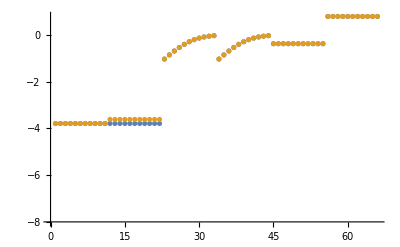

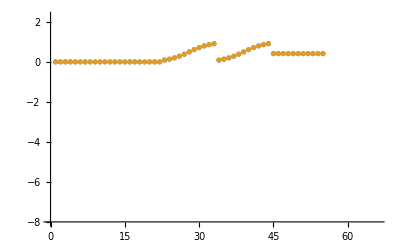

```mathematica
datasetI=10;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet =63;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

{1,1}

{fdp^c→∞}

fdp^c

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{fdp^c→(0.00742751 (4.52597×10^29+1.02536×10^32 cit^c))/(1.67872×10^32+4.70406×10^29 cit^c)}}

{1,1}

{fdp^c→∞}

fdp^c

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{fdp^c→0.0000699269}}

data value | predicted value | error in %
0.00002 | 0.0000200252 | 0.126211
0.00007 | 0.0000699269 | 0.104479

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
0.217 | 0.159464 | 26.5143
3.17 | 2.1908 | 30.8897

```mathematica
backCalculateRatios[haldaneRatiosList, {KeqList[[1]][[3]],KeqList[[1]][[3]]}, paramFitSub]//TableForm
```

data value | predicted value | error in %
0.00016
0.00016 | 0.000336501
0.00022521 | 110.313
40.756

#### Export rate back calculated parameter error distribution

```mathematica
Get["MASSef`"]
```

```mathematica
kmList
```

{{5,fdp,0.00002,{0.000018,0.000022},{},M,8,30,{{trishcl,0.05}},{}},{5,fdp,0.00007,{0.000058,0.000082},{{cit,0.011}},M,8,30,{{trishcl,0.05}},{}}}

```mathematica
assumedSaturatingConc
```

1

```mathematica
Get["MASSef`"]
```

```mathematica
fitLabel
```

new_lma_1

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;

nRateSets=100;
rateConstList=Import["/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/output/treated_data/rateconst_FBA1_"<>fitLabel<>"_"<>flagFitType<>".csv", "TSV"];

predictedParamsErrorList=Table[

(*paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];*)
paramFitSub=Thread[rateConstsSub[[All,1]]->rateConstList[[rateSetI,2;;]]];

{filteredDataList[[rateSetI,1]],
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName][[2;;,3]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2;;,3]],
backCalculateRatios[haldaneRatiosList, {KeqList[[1]][[3]],KeqList[[1]][[3]]},  paramFitSub][[2;;,3]]}//Flatten,
{rateSetI, 1, nRateSets}];

predictedParamsErrorList=Insert[predictedParamsErrorList,{"ssd","Km","Km_cit","kcat", "kcat_cit","Keq", "Keq_cit"} , 1];
predictedParamsErrorList=Insert[predictedParamsErrorList,{0,kmList[[1]][[3]],kmList[[2]][[3]],kcatList[[1]][[3]],kcatList[[2]][[3]], KeqList[[1]][[3]],  KeqList[[1]][[3]]}  ,2];;
Export[outputPath<>"/treated_data/predicted_params_error_distribution_"<>fitLabel<>"_"<>flagFitType<>".csv",predictedParamsErrorList,"CSV"];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

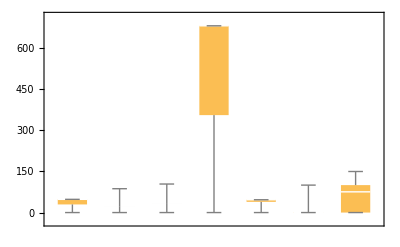

```mathematica
BoxWhiskerChart[Transpose@predictedParamsErrorList[[3;;50,All]]]
```

```mathematica
outputPath<>"/treated_data/predicted_params_error_distribution.csv"
```

/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/output/treated_data/predicted_params_error_distribution.csv

#### Export rate back calculated parameter distribution

```mathematica
nRateSets=100;
predictedParamsList=Table[

paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];
{filteredDataList[[rateSetI,1]],
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName][[2;;,2]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2;;,2]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,2]]}//Flatten,

{rateSetI, 1, nRateSets}];

predictedParamsList=Insert[predictedParamsList,{"ssd","Km_fdp1","Km_fdp2","kcat_f1", "kcat_f2","Keq"} , 1];
predictedParamsList=Insert[predictedParamsList,{"Null",kmList[[1]][[3]],kmList[[2]][[3]],kcatList[[1]][[3]],kcatList[[2]][[3]], KeqList[[1]][[3]]}  ,2];
Export[outputPath<>"/treated_data/predicted_params_distribution.csv",predictedParamsList,"CSV"];
```

Part::partd: Part specification … is longer than depth of object.

ReplaceAll::reps: {enzymeSub} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification … is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ReplaceAll::reps: {enzymeSub} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.